# Notebook for : Simple analytic example of the gravitational wave memory effect by Chakraborty and Kar

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 23, 2022

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article

```mathematica
Hyperlink["Simple analytic example of the gravitational wave memory effect by Chakraborty and Kar",
"https://arxiv.org/abs/2202.10661"]
```

[Simple analytic example of the gravitational wave memory effect by Chakraborty and Kar](https://arxiv.org/abs/2202.10661)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 1696 Kb

{Utilities`CleanSlate`,VariationalMethods`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
<<Notation`
```

```mathematica
Symbolize[A_+]
```

```mathematica
Symbolize[Subscript[A, x]]
```

```mathematica
CreatePalette[{ 
PasteButton[SubPlus[A]],
PasteButton[Subscript[A,x]]
} ]
```

3u9w2_shm38FrontEndObject[LinkObject["3u9w2_shm", 3, 1]]38Untitled-3

```mathematica
Hyperlink["See notebook subscripted variables 101",
"https://community.wolfram.com/groups/-/m/t/306808?sortMsg=Replies"]
```

[See notebook subscripted variables 101](https://community.wolfram.com/groups/-/m/t/306808?sortMsg=Replies)

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 4 Brinkmann Coordinates

```mathematica
Clear[eq4]
eq4 = 
-H[u,x,y] du^2- 2 du dv + dx^2+ dy^2
```

-2 du dv+dx^2+dy^2-du^2 H[u,x,y]

```mathematica
Clear[metric4]
metric4 = 
lineToMetric[ eq4 , {du,dv,dx,dy}]  ;
metric4 // MatrixForm
```

(-H[u,x,y] | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Calculation of Tensors Associated With Metric 4 Brinkmann Coordinates

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;  
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 10.8 for all tensors  *) 
input[ "metric4", metric4, "Brinkmann","g^wp",{u,v,x,y}, "Greek"] // Timing
```

{1.34314,Null}

```mathematica
tensorList
```

{(g^wp)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^wp)_αβ^

Brinkmann

(-H(u,x,y) | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolBrinkmann

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(1/2 (∂H(u,x,y))/(∂u)
0
1/2 (∂H(u,x,y))/(∂x)
1/2 (∂H(u,x,y))/(∂y)) | (0
0
0
0) | (1/2 (∂H(u,x,y))/(∂x)
0
0
0) | (1/2 (∂H(u,x,y))/(∂y)
0
0
0)
(1/2 (∂H(u,x,y))/(∂x)
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(1/2 (∂H(u,x,y))/(∂y)
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorBrinkmann

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 (∂^2 H(u,x,y))/(∂x^2) | 1/2 (∂^2 H(u,x,y))/(∂x ∂y)
0 | 0 | 0 | 0
-1/2 (∂^2 H(u,x,y))/(∂x^2) | 0 | 0 | 0
-1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0) | (0 | 0 | 1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 1/2 (∂^2 H(u,x,y))/(∂y^2)
0 | 0 | 0 | 0
-1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0
-1/2 (∂^2 H(u,x,y))/(∂y^2) | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | -1/2 (∂^2 H(u,x,y))/(∂x^2) | -1/2 (∂^2 H(u,x,y))/(∂x ∂y)
0 | 0 | 0 | 0
1/2 (∂^2 H(u,x,y))/(∂x^2) | 0 | 0 | 0
1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | -1/2 (∂^2 H(u,x,y))/(∂x ∂y) | -1/2 (∂^2 H(u,x,y))/(∂y^2)
0 | 0 | 0 | 0
1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0
1/2 (∂^2 H(u,x,y))/(∂y^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorBrinkmann

(1/2 ((∂^2 H(u,x,y))/(∂x^2)+(∂^2 H(u,x,y))/(∂y^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarBrinkmann

0

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarBrinkmann

0

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorBrinkmann

(1/2 ((∂^2 H(u,x,y))/(∂x^2)+(∂^2 H(u,x,y))/(∂y^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorBrinkmann

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/4 ((∂^2 H(u,x,y))/(∂x^2)-(∂^2 H(u,x,y))/(∂y^2)) | 1/2 (∂^2 H(u,x,y))/(∂x ∂y)
0 | 0 | 0 | 0
1/4 ((∂^2 H(u,x,y))/(∂y^2)-(∂^2 H(u,x,y))/(∂x^2)) | 0 | 0 | 0
-1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0) | (0 | 0 | 1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 1/4 ((∂^2 H(u,x,y))/(∂y^2)-(∂^2 H(u,x,y))/(∂x^2))
0 | 0 | 0 | 0
-1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0
1/4 ((∂^2 H(u,x,y))/(∂x^2)-(∂^2 H(u,x,y))/(∂y^2)) | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 1/4 ((∂^2 H(u,x,y))/(∂y^2)-(∂^2 H(u,x,y))/(∂x^2)) | -1/2 (∂^2 H(u,x,y))/(∂x ∂y)
0 | 0 | 0 | 0
1/4 ((∂^2 H(u,x,y))/(∂x^2)-(∂^2 H(u,x,y))/(∂y^2)) | 0 | 0 | 0
1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | -1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 1/4 ((∂^2 H(u,x,y))/(∂x^2)-(∂^2 H(u,x,y))/(∂y^2))
0 | 0 | 0 | 0
1/2 (∂^2 H(u,x,y))/(∂x ∂y) | 0 | 0 | 0
1/4 ((∂^2 H(u,x,y))/(∂y^2)-(∂^2 H(u,x,y))/(∂x^2)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorBrinkmann

((0
0
1/2 ((∂^3 H(u,x,y))/(∂x ∂y^2)+(∂^3 H(u,x,y))/(∂x^3))
1/2 ((∂^3 H(u,x,y))/(∂x^2 ∂y)+(∂^3 H(u,x,y))/(∂y^3))) | (0
0
0
0) | (1/2 (-(∂^3 H(u,x,y))/(∂x ∂y^2)-(∂^3 H(u,x,y))/(∂x^3))
0
0
0) | (1/2 (-(∂^3 H(u,x,y))/(∂x^2 ∂y)-(∂^3 H(u,x,y))/(∂y^3))
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Derivation of Vacuum Field Equations

```mathematica
Clear[nonzeroRicci] 
nonzeroRicci = 
Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]] ;
nonzeroRicci // TableForm // pdConv
```

1/2 ((∂^2 H(u,x,y))/(∂x^2)+(∂^2 H(u,x,y))/(∂y^2))

```mathematica
Clear[nonzeroEinstein] 
nonzeroEinstein = 
Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]] ;
nonzeroEinstein // TableForm // pdConv
```

1/2 ((∂^2 H(u,x,y))/(∂x^2)+(∂^2 H(u,x,y))/(∂y^2))

```mathematica
Clear[eq5]
eq5 = 
nonzeroRicci[[1]][[2]] ;
eq5 // pdConv
```

(∂^2 H(u,x,y))/(∂x^2)+(∂^2 H(u,x,y))/(∂y^2)

```mathematica
Clear[eq6]
eq6 = 
H[u,x,y] == 1/2 SubPlus[A][u](x^2-y^2) + Subscript[A, x][u] x y
```

H[u,x,y]==1/2 (x^2-y^2) A_+[u]+x y A_x[u]

```mathematica
Clear[hDerivatives]
hDerivatives = { 
D[eq6 ,u] ,
D[eq6 ,x] , 
D[eq6 ,y] ,
D[eq6,{x,2}]  , 
D[eq6,{y,2}]  , 
D[eq6,x,y]
}  /. Equal-> Rule ;
hDerivatives  // TableForm
```

H^(1,0,0)[u,x,y]→1/2 (x^2-y^2) A_+'[u]+x y A_x'[u]
H^(0,1,0)[u,x,y]→x A_+[u]+y A_x[u]
H^(0,0,1)[u,x,y]→-y A_+[u]+x A_x[u]
H^(0,2,0)[u,x,y]→A_+[u]
H^(0,0,2)[u,x,y]→-A_+[u]
H^(0,1,1)[u,x,y]→A_x[u]

```mathematica
(*  Check that general solution satisfies field equations *) 
eq5  /. hDerivatives
```

0

```mathematica
Clear[eq7]
eq7 = { 
tensorList[[3]][-x,-u,-x,-u] /. hDerivatives , 
        tensorList[[3]][-y,-u,-y,-u] /. hDerivatives , 
        tensorList[[3]][-x,-u,-y,-u] /. hDerivatives
} ;
eq7  // TableForm
```

(A_+[u])/2
-1/2 A_+[u]
A_x[u]/2

```mathematica
Clear[Θ] (* [esc]Theta[esc] *) 
Θ[u_]:= 
HeavisideTheta[u]
```

```mathematica
Clear[eq8]
eq8 = 
SubPlus[A][u] == 2 Subscript[A, 0]^2 ( Θ[u+a] - Θ[u-a])
```

A_+[u]==2 (-HeavisideTheta[-a+u]+HeavisideTheta[a+u]) A_0^2

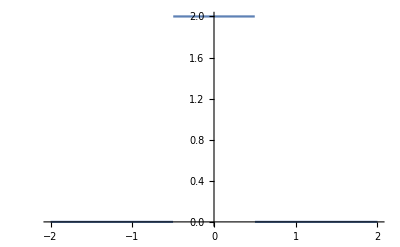

```mathematica
Plot[Evaluate[( eq8[[2]] /. a-> 0.5  /. Subscript[A, 0]-> 1 )  ],{u,-2,2}]
```

## Euler Lagrange Equations and Derivation of Geodesic Equations (Need To Finish Equations 12 and 13)

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{q,qReplace,ℒ,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try using this:

/.q_[λ] :> q 

*)
```

```mathematica
(* Notice that they have used u as an affine parameter *) 
Clear[geodesicEquations]
geodesicEquations = 
eulerLagrangeEquations[metric4,{u,v,x,y} , u ] ;
geodesicEquations // TableForm  // pdConv
```

(∂^2 u(u))/(∂u^2)==0
(∂^2 v(u))/(∂u^2)==1/2 (((∂u(u))/(∂u))^2 (-(∂H(u(u),x(u),y(u)))/(∂u(u)))-2 (∂u(u))/(∂u) (∂x(u))/(∂u) (∂H(u(u),x(u),y(u)))/(∂x(u))-2 (∂u(u))/(∂u) (∂y(u))/(∂u) (∂H(u(u),x(u),y(u)))/(∂y(u)))
(∂^2 x(u))/(∂u^2)==-1/2 ((∂u(u))/(∂u))^2 (∂H(u(u),x(u),y(u)))/(∂x(u))
(∂^2 y(u))/(∂u^2)==-1/2 ((∂u(u))/(∂u))^2 (∂H(u(u),x(u),y(u)))/(∂y(u))

```mathematica
Clear[eq9a]
eq9a = 
geodesicEquations[[3]] /.q_[u] :> q
```

x''==-1/2 (u')^2 H^(0,1,0)[u,x,y]

```mathematica
Clear[eq9]
eq9 = 
eq9a  /. hDerivatives /. u' -> 1
```

x''==1/2 (-x A_+[u]-y A_x[u])

```mathematica
Clear[eq10a]
eq10a = 
geodesicEquations[[4]] /.q_[u] :> q
```

y''==-1/2 (u')^2 H^(0,0,1)[u,x,y]

```mathematica
Clear[eq10]
eq10 = 
eq10a  /. hDerivatives /. u' -> 1
```

y''==1/2 (y A_+[u]-x A_x[u])

```mathematica
Clear[eq11a]
eq11a = 
geodesicEquations[[2]] /.q_[u] :> q
```

v''==1/2 (-2 u' y' H^(0,0,1)[u,x,y]-2 u' x' H^(0,1,0)[u,x,y]-(u')^2 H^(1,0,0)[u,x,y])

```mathematica
Clear[eq11]
eq11 = 
Collect[ ( eq11a  /. hDerivatives /. u' -> 1 // Expand ) ,{SubPlus[A]'[u],SubPlus[A][u],Subscript[A, x]'[u],Subscript[A, x][u]} ]
```

v''==A_x[u] (-y x'-x y')+A_+[u] (-x x'+y y')+(-x^2/4+y^2/4) A_+'[u]-1/2 x y A_x'[u]

```mathematica
Clear[eq14]
eq14 = 
eq9  /. Subscript[A, x][u]-> 0
```

x''==-1/2 x A_+[u]

```mathematica
Clear[eq15]
eq15 = 
eq10  /. Subscript[A, x][u]-> 0
```

y''==1/2 y A_+[u]